POLYMERIZATION TIPS
0<l without a cap

```mathematica
EnPT[p_]:=(-(-2+p+p^2) Log[2,1-p]+p (-p Log[2,4]+(2+p) Log[2,p]))/(-2+p)
h[τ_]:=1/(1+1/τ)
```

POLYMERIZATION

```mathematica
ENP[p_]:=-(Log[2,1-p]+p/(1-p)*Log[2,p])
```

ORDERED

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

```mathematica
ENO[L_,p_]:=-(Sum[P1[l,p]*Log[2,P1[l,p]],{l,0,L-1}]+p^L*Log[2,p^L])
```

COMPETITION

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
S1[c_,p_]:=Sum[P1[l,p]*Log[2,P1[l,p]],{l,0,c-1}]
```

```mathematica
S2[L_,c_,p_]:=Sum[P2[l,p]*Log[2,P2[l,p]],{l,c,L-1}]
ENC[L_,c_,p_]:= -(S1[c,p]+2*S2[L,c,p]+2*P3[L,p]*Log[2,P3[L,p]])
```

PARTIALLY ORDERED

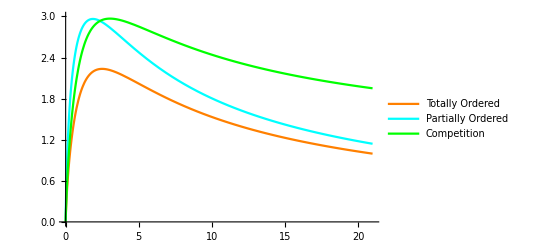

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+c*γ))^(l1+l2)((c*γ)/(2+c*γ))^c

P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*(c*γ)^c/(c*γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*(c*γ)^c/(c*γ+2)^(l1+l2+c),{l2,0,L2-1}]

P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]

ENPO[L1_,L2_,c_,γ_]:=-Sum[Sum[P1[l1,l2,c,γ]*Log[2,P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ]*Log[2, P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ]*Log[2, P2[l2,L1,c,γ]],{l2,0,L2-1}]-P3[L1,L2,c,γ]*Log[2, P3[L1,L2,c,γ]]
G1=Plot[{ENO[4,h[x]],ENPO[4,1,1,1/x],ENC[4,1,h[x]]},{x,0,21},PlotRange->{0,3},PlotStyle->{Orange,Cyan,Green},PlotLegends->{"Totally Ordered","Partially Ordered","Competition"}]
```

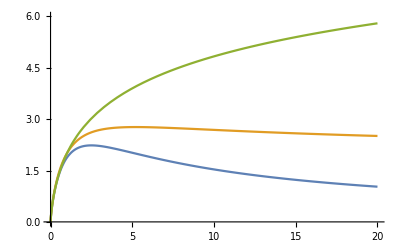

```mathematica
Plot[{ENO[4,h[x]],EnPT[h[x]],ENP[h[x]]},{x,0,20},PlotRange->{0,6}]
```

```mathematica
Export["Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Competition.txt",Cases[Plot[{ENC[4,1,h[x]]},{x,0,200}],Line@x__->x,Infinity],"Table"]
```

Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Competition.txt

```mathematica
Export["Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Polymerizing_Tips.txt",Cases[Plot[{EnPT[h[x]],ENP[h[x]]},{x,0,200}],Line@x__->x,Infinity],"Table"]
```

Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Polymerizing_Tips.txt

```mathematica
Export["Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Ordered.txt",Cases[Plot[{ENO[4,h[x]]},{x,0,200}],Line@x__->x,Infinity],"Table"]
```

Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Ordered.txt

```mathematica
Export["Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Polymerizing.txt",Cases[Plot[ENP[h[x]],{x,0,200}],Line@x__->x,Infinity],"Table"]
```

Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Polymerizing.txt

```mathematica
Export["Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Partial_Order.txt",Cases[Plot[ENPO[4,1,1,1/x],{x,0,200}],Line@x__->x,Infinity],"Table"]
```

Documents/Paper/Paper_Draft_07_11/Images/Figure_2/Partial_Order.mat